#### Import MGenPackage

```mathematica
Block[{$Path=Append[$Path,NotebookDirectory[]]},
<<MGenPackage`]
```

#### Try with less LSTM layers in hope that no overfitting will occur

```mathematica
net2=NetInitialize@NetChain[{
UnitVectorLayer[],
LongShortTermMemoryLayer[30,"Dropout"->0.2],
SequenceLastLayer[],
LinearLayer[64],
Tanh,
LinearLayer[],
SoftmaxLayer[]},
"Input"->NetEncoder[{"Characters",characters}],
"Output"->NetDecoder[{"Class",characters}]
]
```

NetChain[]

```mathematica
trainedNet2=net2;
```

```mathematica
trainedNet2=NetTrain[trainedNet2,trainingData,BatchSize->512,TargetDevice->"CPU",MaxTrainingRounds->Quantity[1,"Hours"],TrainingProgressCheckpointing->{"Directory","~/Desktop/slask/FluteCheckpoints2"}]
```

NetChain[]

#### Yes, this will be more new material and not so much from the original sequence

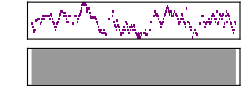

```mathematica
fromCodedNoteString[generateSample[trainedNet2,"+c+a+S+R+S e+++f+++++",500],100]
```

```mathematica
trainedNet2=Import[FileNameJoin[{NotebookDirectory[],"FluteNets","2017-09-21T17:38:19_13_017_00321_5.73e-1.wlnet"}]]
```

NetChain[]

```mathematica
{#,toWAVSound[#]}&/@(fromCodedNoteString[generateSample[trainedNet3,#,500],90]&/@{"    ","    ","ancdef","abcdef","S++ R++ Q++"})
```

#### Export MIDI file

```mathematica
Export["/tmp/a.mid",%]
```

/tmp/a.mid

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["/tmp/a.mid"]]]
```

#### Now, may we need some more data to learn from. Maybe on a bit larger net.